```mathematica
max=1000
```

1000

```mathematica
S1[b_]:=Block[{next=b,result={}},
If[Mod[b,3]==2,
While[next<max&&Mod[next,3]==2,
AppendTo[result,next];
next=(2 next-1)/3
];
];
result
]
```

```mathematica
S1[8]
```

8

5

{8,5}

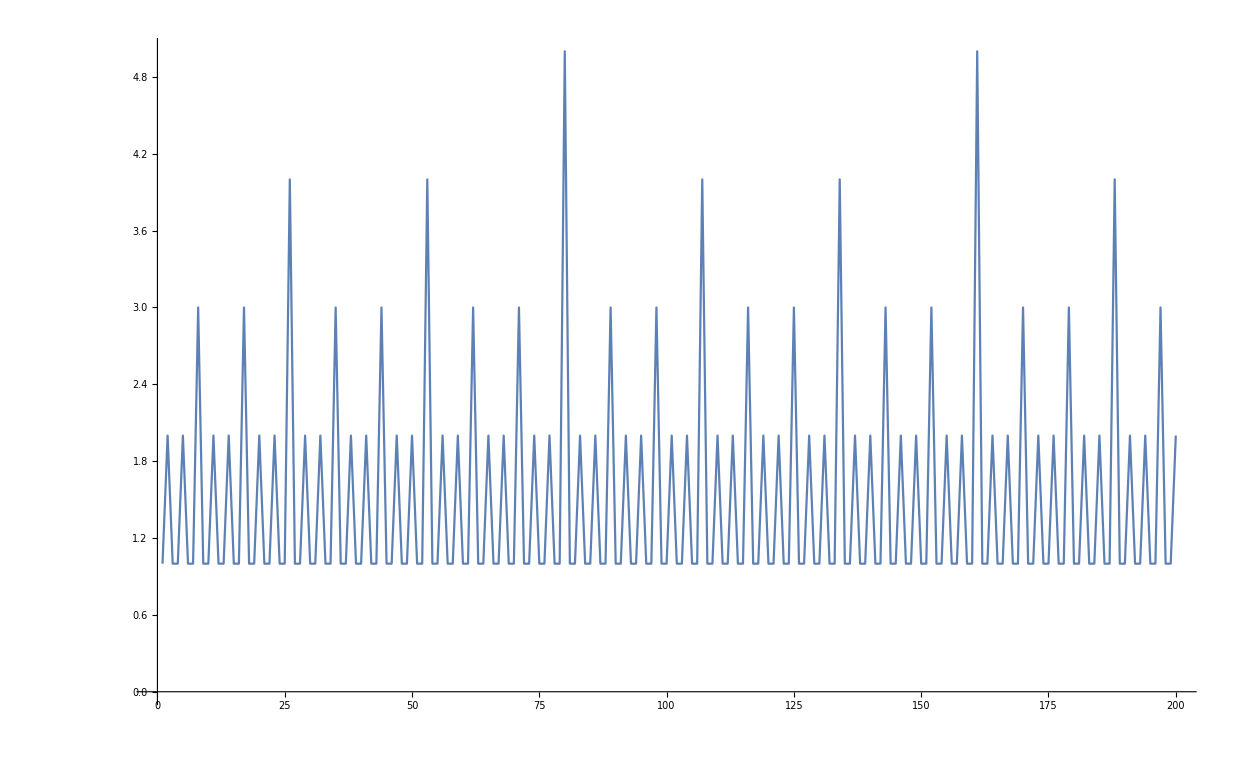

```mathematica
ListLinePlot[Table[S1[k*3+2]//Length,{k,200}],PlotRange->All]
```